```mathematica
wassdist[cdf1_,cdf2_]:=∫_(-∞)^(+∞) Abs[cdf1[x]-cdf2[x]]ⅆx;
```

```mathematica
CDF[NormalDistribution[0,1]][x]
```

1/2 Erfc[-x/(√2)]

```mathematica
CDF[NormalDistribution[0,σ]][x]
```

1/2 Erfc[-x/(√2 σ)]

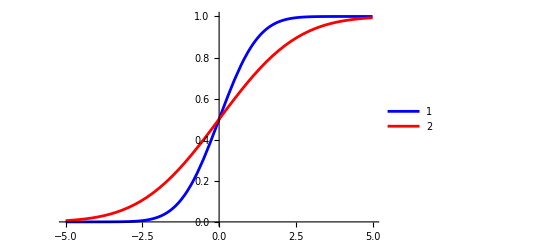

```mathematica
Plot[{CDF[NormalDistribution[0,1]][x],
CDF[NormalDistribution[0,2]][x]},{x,-5,+5},
PlotStyle->{Blue,Red},
PlotLegends->{1,2}]
```

```mathematica
wassdistsym[cdf1_,cdf2_]:=∫_(-∞)^0 (cdf1[x]-cdf2[x])ⅆx+∫_0^(+∞) (cdf2[x]-cdf1[x])ⅆx;
```

```mathematica
wassdist[CDF[NormalDistribution[0,1]],CDF[NormalDistribution[3,2]]]
```

(3 ⅇ^(9/2)+√(2/π)-3 ⅇ^(9/2) Erfc[3/(√2)])/ⅇ^(9/2)

```mathematica
Table[
{σ,wassdist[
CDF[NormalDistribution[0,1]],
CDF[NormalDistribution[0,σ]]],
Abs[(σ-1)√(2/π)]},
{σ,{10^-3,10^-2,10^-1,5 10^-1,10^0,2 10^0,5 10^0,10^1}}]
```

{{1/1000,999/(500 √(2 π)),999/(500 √(2 π))},{1/100,99/(50 √(2 π)),99/(50 √(2 π))},{1/10,9/(5 √(2 π)),9/(5 √(2 π))},{1/2,1/(√(2 π)),1/(√(2 π))},{1,0,0},{2,√(2/π),√(2/π)},{5,4 √(2/π),4 √(2/π)},{10,9 √(2/π),9 √(2/π)}}

```mathematica
Table[
{σ,wassdist[
CDF[NormalDistribution[0,2]],
CDF[NormalDistribution[0,σ]]],
Abs[(σ-2)√(2/π)]},
{σ,{10^-3,10^-2,10^-1,5 10^-1,10^0,2 10^0,5 10^0,10^1}}]
```

{{1/1000,1999/(500 √(2 π)),1999/(500 √(2 π))},{1/100,199/(50 √(2 π)),199/(50 √(2 π))},{1/10,19/(5 √(2 π)),19/(5 √(2 π))},{1/2,3/(√(2 π)),3/(√(2 π))},{1,√(2/π),√(2/π)},{2,0,0},{5,3 √(2/π),3 √(2/π)},{10,8 √(2/π),8 √(2/π)}}

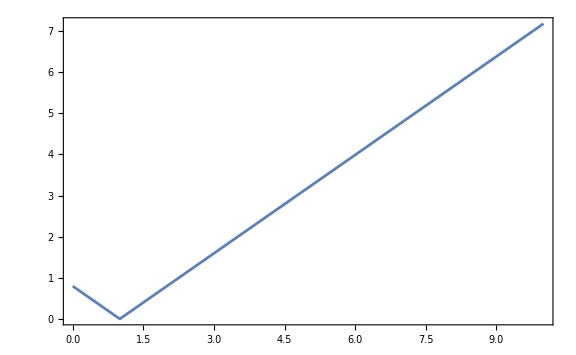

```mathematica
DiscretePlot[
wassdist[
CDF[NormalDistribution[0,1]],
CDF[NormalDistribution[0,σ]]],
{σ,{10^-3,10^-2,10^-1,5 10^-1,10^0,2 10^0,5 10^0,10^1}},
Frame->True,PlotRange->All,ImageSize->Large,
Filling->None,Joined->True]
```

```mathematica
wassdistN[cdf1_,cdf2_]:=NIntegrate[Abs[cdf1[x]-cdf2[x]],{x,-∞,+∞}];
```

```mathematica
Table[
{σ,wassdistN[
CDF[NormalDistribution[0,2]],
CDF[NormalDistribution[0,σ]]],
1.Abs[(σ-2)√(2/π)]},
{σ,{10^-3,10^-2,10^-1,5 10^-1,10^0,2 10^0,5 10^0,10^1}}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{1/1000,1.59577,1.59497},{1/100,1.58779,1.58779},{1/10,1.51598,1.51598},{1/2,1.19683,1.19683},{1,0.797885,0.797885},{2,0.,0.},{5,2.39365,2.39365},{10,6.38308,6.38308}}

```mathematica
wassdist[CDF[StudentTDistribution[0,1,3]],CDF[StudentTDistribution[0,1,1]]]
```

∞

```mathematica
CDF[StudentTDistribution[0,1,1]][x]
```

1/2+ArcTan[x]/π

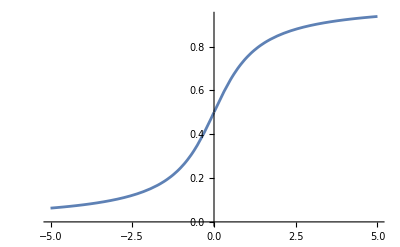

```mathematica
Plot[CDF[StudentTDistribution[0,1,1]][x],{x,-5,+5}]
```

```mathematica
Variance[StudentTDistribution[0,1,ν]]
```

Piecewise[{{ν/(-2+ν), ν>2}, {Indeterminate, True}}]

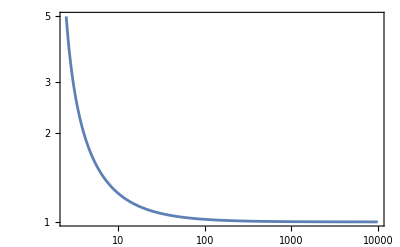

```mathematica
LogLogPlot[ν/(-2+ν),{ν,2.5,10000},Frame->True,PlotRange->All]
```

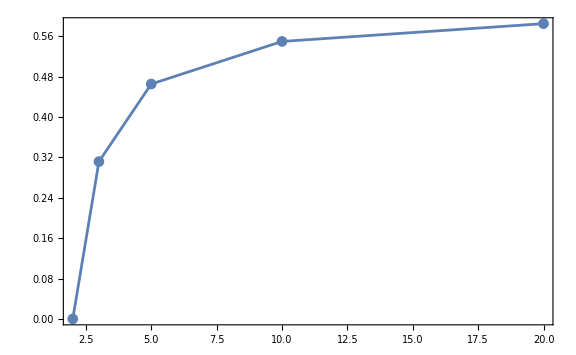

```mathematica
DiscretePlot[
wassdistN[
CDF[StudentTDistribution[0,1,2]],
CDF[StudentTDistribution[0,1,ν]]],
{ν,{2,3,5,10,20}},
Frame->True,PlotRange->All,ImageSize->Large,
PlotMarkers->Automatic,Filling->None,Joined->True]
```

```mathematica
{Variance[StudentTDistribution[0,1,3]],Variance[StudentTDistribution[0,1,6]]}
```

{3,3/2}

```mathematica
{Variance[NormalDistribution[0,3^(1/2)]],Variance[NormalDistribution[0,(3/2)^(1/2)]]}
```

{3,3/2}

```mathematica
{wassdistN[CDF[StudentTDistribution[0,1,3]],CDF[StudentTDistribution[0,1,6]]],wassdistN[CDF[NormalDistribution[0,3^(1/2)]],CDF[NormalDistribution[0,(3/2)^(1/2)]]]}
```

{0.184099,0.404772}

```mathematica
wassdistNz[cdf1_,cdf2_,z_]:=NIntegrate[Abs[cdf1[x]-cdf2[x]],{x,-∞,z}];
```

```mathematica
percwas=Table[{z,
wassdistNz[CDF[StudentTDistribution[0,1,3]],CDF[StudentTDistribution[0,1,6]],z]/
wassdistN[CDF[StudentTDistribution[0,1,3]],CDF[StudentTDistribution[0,1,6]]],
wassdistNz[CDF[NormalDistribution[0,3^(1/2)]],CDF[NormalDistribution[0,(3/2)^(1/2)]],z]/
wassdistN[CDF[NormalDistribution[0,3^(1/2)]],CDF[NormalDistribution[0,(3/2)^(1/2)]]]},
{z,Range[-6,6]}]
```

{{-6,0.0757347,0.000288213},{-5,0.104028,0.00241096},{-4,0.149011,0.0148042},{-3,0.221975,0.0652622},{-2,0.333037,0.198206},{-1,0.45386,0.395449},{0,0.5,0.5},{1,0.54614,0.604551},{2,0.666963,0.801794},{3,0.778025,0.934738},{4,0.850989,0.985196},{5,0.895972,0.997589},{6,0.924265,0.999712}}

StT : 1/3 between - 2 and +2
Gauss: 3/5 between -2 and +2

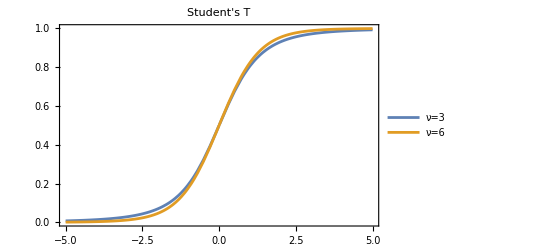

```mathematica
Plot[{CDF[StudentTDistribution[0,1,3]][x],CDF[StudentTDistribution[0,1,6]][x]},{x,-5,+5},
Frame->True,PlotRange->All,PlotLabel->"Student's T",PlotLegends->{"ν=3","ν=6"}]
```

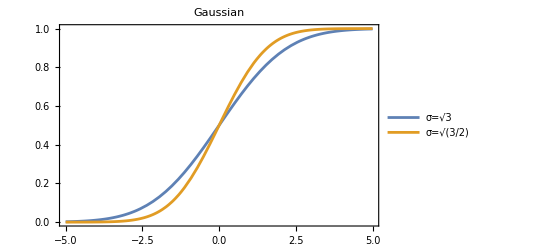

```mathematica
Plot[{CDF[NormalDistribution[0,3^(1/2)]][x],CDF[NormalDistribution[0,(3/2)^(1/2)]][x]},{x,-5,+5},
Frame->True,PlotRange->All,PlotLabel->"Gaussian",PlotLegends->{"σ=√3","σ=√(3/2)"}]
```

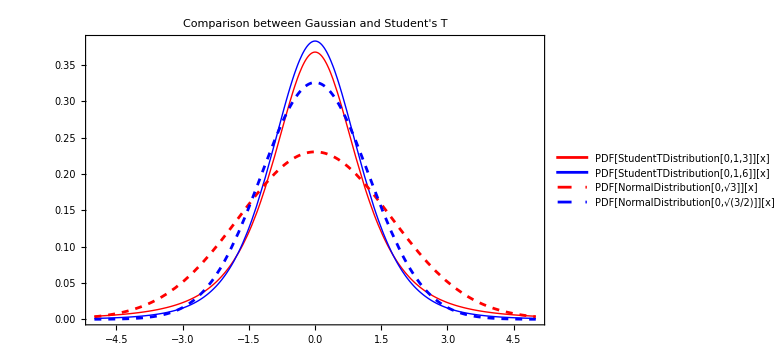

```mathematica
Plot[{PDF[StudentTDistribution[0,1,3]][x],PDF[StudentTDistribution[0,1,6]][x],
PDF[NormalDistribution[0,3^(1/2)]][x],PDF[NormalDistribution[0,(3/2)^(1/2)]][x]},{x,-5,+5},
Frame->True,PlotRange->All,PlotLegends->"Expressions",ImageSize->Large,
PlotStyle->{{Red,Thick},{Blue,Thick},{Red,Dashed},{Blue,Dashed}},
PlotLabel->"Comparison between Gaussian and Student's T"]
```

```mathematica
wassdist[CDF[StudentTDistribution[0,1,3]],CDF[StudentTDistribution[0,1,2]]]
```

(-2 √3+√2 π)/π

```mathematica
wassdistN[CDF[StudentTDistribution[0,1,3]],CDF[StudentTDistribution[0,1,1.9]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-6.3887×10^56}. NIntegrate obtained 1.47874×10^228 and 1.45757×10^228 for the integral and error estimates.

1.47874×10^228

```mathematica
wassdistN[CDF[StudentTDistribution[0,1,3]],CDF[StudentTDistribution[0,1,2]]]
```

0.311556

```mathematica
wassdist[CDF[StudentTDistribution[0,1,3]],CDF[StudentTDistribution[0,1,3]]]
```

0

```mathematica
wassdistN[CDF[StudentTDistribution[0,1,3]],CDF[StudentTDistribution[0,1,4]]]
```

0.102658

```mathematica
datagauss=Table[{σ-1,wassdistN[CDF[NormalDistribution[0,1]],CDF[NormalDistribution[0,σ]]]},{σ,{1,2,3,4,5}}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0,0.},{1,0.797885},{2,1.59577},{3,2.39365},{4,3.19154}}

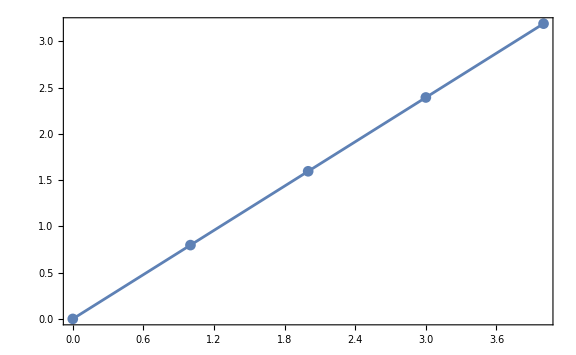

```mathematica
ListLinePlot[datagauss,Frame->True,PlotRange->All,
ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
Variance[StudentTDistribution[0,1/(√3),3]]
```

1

```mathematica
Timing[datastt=Table[{√(3/(3-2))-√(ν/(ν-2)),wassdistN[CDF[StudentTDistribution[0,1/(√3),3]],CDF[StudentTDistribution[0,1/(√3),ν]]]},{ν,{3,4,5,6,7,8,9,10,20,30,50,100,1000,10000}}]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{34.2634,{{0,0.},{-√2+√3,0.0592695},{-√(5/3)+√3,0.0887047},{-√(3/2)+√3,0.10629},{-√(7/5)+√3,0.117978},{-2/(√3)+√3,0.126309},{√3-3/(√7),0.132548},{√3-(√5)/2,0.137393},{√3-(√10)/3,0.157737},{-√(15/14)+√3,0.16403},{√3-5/(2 √6),0.168904},{-(5 √2)/7+√3,0.17247},{-10 √(5/499)+√3,0.175615},{-50 √(2/4999)+√3,0.175926}}}

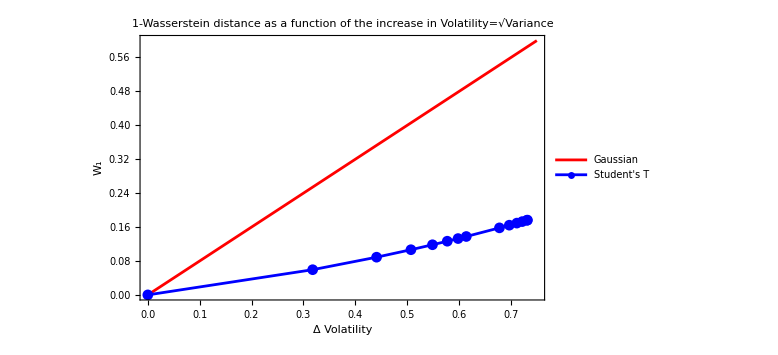

```mathematica
Show[
Plot[√(2/π)x,{x,0,0.75},PlotStyle->Red,Frame->True,
PlotRange->All,ImageSize->Large,PlotLegends->{"Gaussian"},
PlotLabel->"1-Wasserstein distance as a function of the increase in Volatility=√Variance",
FrameLabel->{"Δ Volatility","W_1"}],
ListLinePlot[datastt,Frame->True,PlotRange->All,
ImageSize->Large,PlotMarkers->Automatic,PlotStyle->Blue,
PlotLegends->{"Student's T"}]]
```

```mathematica
datasttgauss=Table[{σ,wassdistN[CDF[StudentTDistribution[0,1,10000]],CDF[StudentTDistribution[0,σ,10000]]]},{σ,{10^-3,10^-2,10^-1,2 10^-1,5 10^-1,9 10^-1,10^0,1.1 10^0,1.5 10^0,2 10^0,5 10^0,8 10^0,10^1}}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{1/1000,0.797944},{1/100,0.789965},{1/10,0.71815},{1/5,0.638356},{1/2,0.398972},{9/10,0.0797944},{1,0.},{1.1,0.0797944},{1.5,0.398972},{2,0.797944},{5,3.19178},{8,5.58561},{10,7.1815}}

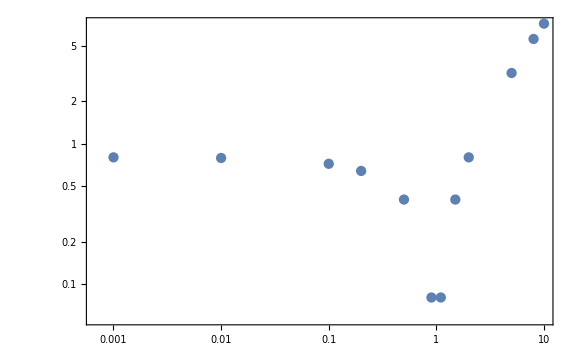

```mathematica
ListLogLogPlot[datasttgauss,Frame->True,PlotRange->All,ImageSize->Large]
```

```mathematica
datapareto=Table[{α,wassdistN[CDF[ParetoDistribution[1,3]],CDF[ParetoDistribution[1,α]]]},{α,{1.1,1.25,1.5,1.75,2,2.25,2.5,2.75,3,3.25,3.5,3.75,4,4.5,5,8,10,20,50,100}}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{1.1,9.5},{1.25,3.5},{1.5,1.5},{1.75,0.833333},{2,0.5},{2.25,0.3},{2.5,0.166667},{2.75,0.0714286},{3,0.},{3.25,0.0555556},{3.5,0.1},{3.75,0.136364},{4,0.166667},{4.5,0.214286},{5,0.25},{8,0.357143},{10,0.388889},{20,0.447368},{50,0.479592},{100,0.489899}}

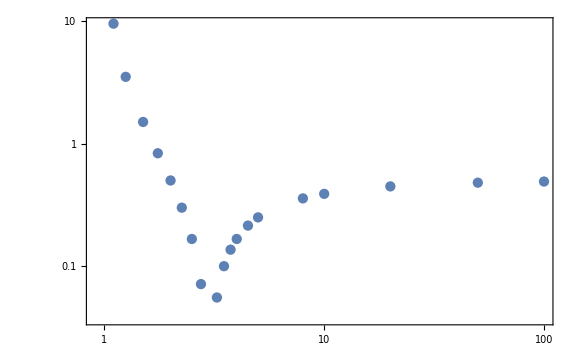

```mathematica
ListLogLogPlot[datapareto,Frame->True,PlotRange->All,ImageSize->Large]
```